```mathematica
Define spin configuration for unit cell (12 spins), the x,y,z component of spin i (i=1,2,..12)
```

```mathematica
dx1=0;
dx2=0;
dx3=0;

X[1]=-1/2+dx2+dx1;
X[2]=1-dx1;
X[3]=-1/2-dx2;
X[4]=-1/2-dx3;
X[5]=1+dx2+dx3;
X[6]=-1/2-dx1+dx3;
X[7]=-1/2-dx3;
X[8]=-1/2-dx2;
X[9]=-1/2+dx2+dx1;
X[10]=1-dx2-dx3;
X[11]=-1/2-dx1+dx3;
X[12]=1+dx1;

ds1=0.29;
ds2=0.2;
ds3=0.17;

Y[1]=-Sqrt[3]/2+ds1+ds2;
Y[2]=-ds1;
Y[3]=Sqrt[3]/2-ds2;
Y[4]=-Sqrt[3]/2-ds3;
Y[5]=ds2+ds3;
Y[6]=-Sqrt[3]/2-ds1+ds3;
Y[7]=Sqrt[3]/2-ds3;
Y[8]=-Sqrt[3]/2-ds2;
Y[9]=Sqrt[3]/2+ds2+ds1;
Y[10]=-ds2-ds3;
Y[11]=Sqrt[3]/2-ds1+ds3;
Y[12]=ds1;

h1=0.5;
h2=0.3;
h3=0.43;

Z[1]=h1+h2;
Z[2]=-h1;
Z[3]=-h2;
Z[4]=0-h3;
Z[5]=h2+h3;
Z[6]=-h1+h3;
Z[7]=0-h3;
Z[8]=-h2;
Z[9]=h1+h2;
Z[10]=-h2-h3;
Z[11]=-h1+h3;
Z[12]=h1;
```

### Calculate the lenght of each spin

```mathematica
For[i=1,i≤12,i++,S[i]=Sqrt[X[i]^2+Y[i]^2+Z[i]^2]];
```

### Calculate the direction unit vector for local spin i, VN is spin direction vector, VN1 is first deviation vector and VN2 is second deviation vector, VN X VN1=VN2

```mathematica
For[i=1,i≤12,i++,VN[i]={X[i],Y[i],Z[i]}/S[i]];
For[i=1,i≤12,i++,VN1[i]={-Y[i],X[i],0}/Sqrt[X[i]^2+Y[i]^2]];
For[i=1,i≤12,i++,VN2[i]=Cross[VN[i],VN1[i]]];
```

### Define the nearneighbor total static spin NSS[i] and deviation spin NDS[i]

```mathematica
Clear[S1,S2,kx,ky]
For[i=1,i≤12,i++,NSS[i]=-2S[i]VN[i]];
NDS[1]=S1[2]VN1[2]+S1[3]VN1[3]+S1[10]VN1[10]+S1[11]VN1[11]+S2[2]VN2[2]+S2[3]VN2[3]+S2[10]VN2[10]+S2[11]VN2[11];
NDS[2]=S1[1]VN1[1]+S1[3]VN1[3]+S1[8]VN1[8]Exp[-I ky Sqrt[3]/2]+S1[9]VN1[9]Exp[-I ky Sqrt[3]/2]+S2[1]VN2[1]+S2[3]VN2[3]+S2[8]VN2[8]Exp[-I ky Sqrt[3]/2]+S2[9]VN2[9]Exp[-I ky Sqrt[3]/2];
NDS[3]=S1[1]VN1[1]+S1[2]VN1[2]+S1[4]VN1[4]+S1[5]VN1[5]+S2[1]VN2[1]+S2[2]VN2[2]+S2[4]VN2[4]+S2[5]VN2[5];
NDS[4]=S1[3]VN1[3]+S1[5]VN1[5]+S1[11]VN1[11]Exp[I kx]+S1[12]VN1[12]Exp[I kx]+S2[3]VN2[3]+S2[5]VN2[5]+S2[11]VN2[11]Exp[I kx]+S2[12]VN2[12]Exp[I kx];
NDS[5]=S1[3]VN1[3]+S1[4]VN1[4]+S1[7]VN1[7]+S1[8]VN1[8]+S2[3]VN2[3]+S2[4]VN2[4]+S2[7]VN2[7]+S2[8]VN2[8];
NDS[6]=S1[7]VN1[7]+S1[9]VN1[9]Exp[I kx]+S1[10]VN1[10]Exp[I kx]+S1[12]VN1[12]Exp[I kx+I ky Sqrt[3]/2]+S2[7]VN2[7]+S2[9]VN2[9]Exp[I kx]+S2[10]VN2[10]Exp[I kx]+S2[12]VN2[12]Exp[I kx +I ky Sqrt[3]/2];
NDS[7]=S1[5]VN1[5]+S1[6]VN1[6]+S1[8]VN1[8]+S1[12]VN1[12]Exp[I kx+I ky Sqrt[3]/2]+S2[5]VN2[5]+S2[6]VN2[6]+S2[8]VN2[8]+S2[12]VN2[12]Exp[I kx+I ky Sqrt[3]/2];
NDS[8]=S1[5]VN1[5]+S1[7]VN1[7]+S1[9]VN1[9]+S1[2]VN1[2]Exp[I ky Sqrt[3]/2]+S2[5]VN2[5]+S2[7]VN2[7]+S2[9]VN2[9]+S2[2]VN2[2]Exp[I ky Sqrt[3]/2];
NDS[9]=S1[8]VN1[8]+S1[10]VN1[10]+S1[2]VN1[2]Exp[I ky Sqrt[3]/2]+S1[6]VN1[6]Exp[-I kx]+S2[8]VN2[8]+S2[10]VN2[10]+S2[2]VN2[2]Exp[I ky Sqrt[3]/2]+S2[6]VN2[6]Exp[-I kx];
NDS[10]=S1[1]VN1[1]+S1[9]VN1[9]+S1[11]VN1[11]+S1[6]VN1[6]Exp[-I kx]+S2[1]VN2[1]+S2[9]VN2[9]+S2[11]VN2[11]+S2[6]VN2[6]Exp[-I kx];
NDS[11]=S1[1]VN1[1]+S1[10]VN1[10]+S1[12]VN1[12]+S1[4]VN1[4]Exp[-I kx]+S2[1]VN2[1]+S2[10]VN2[10]+S2[12]VN2[12]+S2[4]VN2[4]Exp[-I kx];
NDS[12]=S1[11]VN1[11]+S1[4]VN1[4]Exp[-I kx]+S1[6]VN1[6]Exp[-I kx -I ky Sqrt[3]/2]+S1[7]VN1[7]Exp[-I kx-I ky Sqrt[3]/2]+S2[11]VN2[11]+S2[4]VN2[4]Exp[-I kx]+S2[6]VN2[6]Exp[-I kx-I ky Sqrt[3]/2]+S2[7]VN2[7]Exp[-I kx-I ky Sqrt[3]/2];
```

### Define dynamical matrix equations DTS1[i], DTS2[i]

```mathematica
For[i=1,i≤12,i++,DTS1[i]=VN1[i].(S[i]Cross[VN[i],NDS[i]]+S2[i]Cross[VN2[i],NSS[i]])];
For[i=1,i≤12,i++,DTS2[i]=VN2[i].(S[i]Cross[VN[i],NDS[i]]+S1[i]Cross[VN1[i],NSS[i]])];
```

### Define the dynamical Matrix

```mathematica
DNMM=CoefficientArrays[Flatten[Table[{DTS1[i],DTS2[i]},{i,1,12}]]==0,Flatten[Table[{S1[i],S2[i]},{i,1,12}]]][[2]];
Clear[HH];
MatrixForm[DNMM]
```

```mathematica
HH[kx_,ky_]:=-I({{0, -2.0311524849614333, -0.6398917620276308, -0.7718086603104173, 0.7999997115222346, -0.5888226567515378, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.6728274263322982, -0.7607133418660784, 0.7988185121979376, -0.6271013987571694, 0, 0}, {2.031152484961433, 0, -0.6095289089898412, 0.3516453486148766, -0.0008624594215098647, -0.34418285535163373, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.5494082890657395, 0.4825217161634417, -0.05517428971916266, -0.07880191650911575, 0, 0}, {-0.3999323512672692, -0.8777913698055035, 0, -2.3100649341522836, 0.30042970410251596, -0.8441315857146791, 0, 0, 0, 0, 0, 0, 0, 0, -0.4939041998975139 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.989749273032859 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0.4023830213221271 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -1.0546907157240326 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0}, {-0.6932277952712486, 0.7277599944156907, 2.310064934152284, 0, -0.9232806566118109, 0.2352035729522713, 0, 0, 0, 0, 0, 0, 0, 0, -0.1798091587190177 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.28169857421060673 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.6856181821648307 ⅇ^((0.-0.8660254037844386 ⅈ) ky), -0.4501607017906666 ⅇ^((0.-0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0}, {0.29999989182083797, -0.5132351323736012, -0.1802578224615096, -0.6469345665203244, 0, -1.770412198880504, 0.2664865417056206, -0.7318599092949879, -0.2875088945775633, -0.73559018949904, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-0.0007517449783734503, -0.6973032595367855, -0.7075936755240125, -0.23024652042707092, 1.770412198880504, 0, -0.40656273012760413, 0.2753153391158224, -0.252773069868077, 0.47925324224661575, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -0.38196404311138943, -1.0153599535834326, 0, -2.456215493222619, 0.2983408408379977, -1.1241559043731129, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.3708554844340238 ⅇ^((0.+1. ⅈ) kx), -1.1299781650920915 ⅇ^((0.+1. ⅈ) kx), 0.31987973855385593 ⅇ^((0.+1. ⅈ) kx), -1.1613929431982508 ⅇ^((0.+1. ⅈ) kx)}, {0, 0, 0, 0, -0.5640526411520226, -0.3697152408272808, 2.4562154932226195, 0, -0.8844247456964924, -0.4813615050610922, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.6215875850684358 ⅇ^((0.+1. ⅈ) kx), -0.0823073907972427 ⅇ^((0.+1. ⅈ) kx), -0.8207245826691918 ⅇ^((0.+1. ⅈ) kx), -0.3954854950975375 ⅇ^((0.+1. ⅈ) kx)}, {0, 0, 0, 0, -0.699604976805404, -1.0738008887542232, 0.5064856135156706, -1.1828299249675518, 0, -2.584414827383561, 0, 0, -0.703831399174679, -1.039889163007425, 0.512276332502108, -1.161649744887828, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -0.36899342997263906, 0.41970014136863987, -0.9305862750193894, -0.3139123968574027, 2.5844148273835605, 0, 0, 0, -0.3428851390787505, 0.5587347713289829, -0.9206006866846022, -0.22388830159195056, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -2.2155325291299746, -0.062136430942448764, -0.9736876356310353, 0, 0, -0.05130221172915808 ⅇ^((0.+1. ⅈ) kx), -0.9903212454226173 ⅇ^((0.+1. ⅈ) kx), 0.06953827190484141 ⅇ^((0.+1. ⅈ) kx), -0.9077036471497394 ⅇ^((0.+1. ⅈ) kx), 0, 0, 0.05114381876462775 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -1.0172871954332103 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 2.2155325291299746, 0, -0.5101186877409575, -0.4409852798120379, 0, 0, -0.7536671285063908 ⅇ^((0.+1. ⅈ) kx), 0.39317865085369064 ⅇ^((0.+1. ⅈ) kx), -0.12702520834423087 ⅇ^((0.+1. ⅈ) kx), 0.6216767431580479 ⅇ^((0.+1. ⅈ) kx), 0, 0, -0.7563583345056681 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -0.35036366437076544 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, -0.41458561869193417, -0.7716059821926239, 0.38169521864647094, -0.842776237642135, 0, -1.9176562389680694, 0.37543045508278416, -0.7787083482709654, 0, 0, 0, 0, 0, 0, -0.4052857901388009 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), -0.8347384353261367 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0, 0, 0, 0, 0, 0, -0.25442348466537934, 0.5222484639493346, -0.44153370410896076, 0.05378224553118491, 1.9176562389680696, 0, -0.4674783431086357, 0.20669003951346931, 0, 0, 0, 0, 0, 0, -0.32037839267124546 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky), 0.3912095930546387 ⅇ^((0.+1. ⅈ) kx+(0.+0.8660254037844386 ⅈ) ky)}, {0, 0, 0.2963425199385083 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -1.0412008456194037 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0.2105245202063457, -1.0923114492871138, 0, 0, -0.261928224476361, -0.9868191787453886, 0, -2.4301523915292025, -0.21349106486214334, -1.132239803056297, 0, 0, 0, 0, 0, 0}, {0, 0, -0.18915643911984906 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0.5195795385759214 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, -0.8656504894978233, -0.48169881296267836, 0, 0, -0.592412545277087, -0.4757647380863636, 2.4301523915292025, 0, -0.8536487066124647, 0.4187604961788437, 0, 0, 0, 0, 0, 0}, {0, 0, 0.6438128341154034 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -1.508402257470381 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.5863109911903781 ⅇ^((0.-1. ⅈ) kx), -1.476774564793678 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.5693095062990491, -1.5392924814350688, 0, -3.3038189391725155, 0.6079197207273606, -1.4863325708757582, 0, 0, 0, 0}, {0, 0, -0.9805604603527888 ⅇ^((0.+0.8660254037844386 ⅈ) ky), -0.5754819386206328 ⅇ^((0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -1.1238741477512761 ⅇ^((0.-1. ⅈ) kx), 0.0765022478811403 ⅇ^((0.-1. ⅈ) kx), 0, 0, -1.1605448177394648, 0.2902434538238222, 3.303818939172515, 0, -1.0738078909961781, -0.7091418557572811, 0, 0, 0, 0}, {-0.6139550265282221, -0.9679228195142247, 0, 0, 0, 0, 0, 0, 0, 0, -0.7251848355790604 ⅇ^((0.-1. ⅈ) kx), -1.0588347197434902 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0.5547267451637165, -1.1626847612770637, 0, -2.584414827383561, 0.42768848275007576, -1.0170593721220247, 0, 0}, {-0.6990607249144524, 0.8560978014984089, 0, 0, 0, 0, 0, 0, 0, 0, -0.14817468377466436 ⅇ^((0.-1. ⅈ) kx), -0.08111627277802827 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, -0.839987023001651, -0.4755456545993924, 2.5844148273835605, 0, -1.047207083201708, 0.05883056736264283, 0, 0}, {0.06989661981731954, -0.5562335282894889, 0, 0, 0, 0, 0.06037182304739922 ⅇ^((0.-1. ⅈ) kx), -0.8288300864550062 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.04101122437329495, -0.7089996235111111, 0, -1.8016147236207125, -0.06670167738091026, -0.8187671530132578}, {-0.04893911878075751, -0.7085451258495366, 0, 0, 0, 0, -0.45592959916145165 ⅇ^((0.-1. ⅈ) kx), 0.2720195776532676 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -0.7300158162635755, -0.2981448099899727, 1.8016147236207125, 0, -0.27325453294392216, 0.37157497264324785}, {0, 0, 0, 0, 0, 0, 0.37195318436494884 ⅇ^((0.-1. ⅈ) kx), -1.0922873502984747 ⅇ^((0.-1. ⅈ) kx), 0, 0, 0.36531299117591254 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -1.0606928344469908 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.47126254667302436 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -1.0055503950351974 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.4764405527207876, -1.049838938710747, 0, -2.3100649341522836}, {0, 0, 0, 0, 0, 0, -0.7718895529534183 ⅇ^((0.-1. ⅈ) kx), -0.300846146935402 ⅇ^((0.-1. ⅈ) kx), 0, 0, -0.78863065345355 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.053326024679584 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), -0.38593720580919955 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0.488219146416802 ⅇ^((0.-1. ⅈ) kx-(0.+0.8660254037844386 ⅈ) ky), 0, 0, 0, 0, 0, 0, -0.3503722002134384, 0.08552616935607281, 2.310064934152284, 0}})
```

### Dispersion relation E[kx,ky]

```mathematica
EE[kx_,ky_]:=Sort[Re[Eigenvalues[HH[kx,ky]]]];
```

```mathematica
N[EE[0,0]]
```

{-2.90803,-2.83109,-2.31871,-2.14926,-1.54211,-1.45804,-1.05677,-0.944097,-0.0945169,-3.60745×10^-8,-2.15049×10^-8,-1.69292×10^-8,1.69292×10^-8,2.15049×10^-8,3.60745×10^-8,0.0945169,0.944097,1.05677,1.45804,1.54211,2.14926,2.31871,2.83109,2.90803}

### 3D Plot

```mathematica
Plot3D[EE[x,y],{x,-Pi,Pi},{y,- 2Pi/Sqrt[3], 2Pi/Sqrt[3]},AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

```mathematica
Show[%168,ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[{EE[x,y][[11]],EE[x,y][[12]],EE[x,y][[13]],EE[x,y][[14]]},{x,-Pi,Pi},{y,-2Pi/Sqrt[3],2Pi/Sqrt[3]},AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

### 1D High symmetry Brillouin zone point loop plot

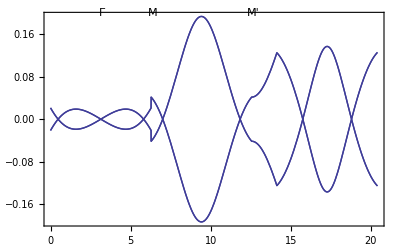

```mathematica
Plot[Piecewise[{{{EE[Pi-t ,(Pi-t)Sqrt[3]/2][[11]],EE[Pi-t ,(Pi-t)Sqrt[3]/2][[12]],EE[Pi-t ,(Pi-t)Sqrt[3]/2][[13]],EE[Pi-t ,(Pi-t)Sqrt[3]/2][[14]]},t≥0&&t<2Pi},{{EE[-Pi,-Pi+(t-2Pi)][[11]],EE[-Pi,-Pi+(t-2Pi)][[12]],EE[-Pi,-Pi+(t-2Pi)][[13]],EE[-Pi,-Pi+(t-2Pi)][[14]]},t≥2Pi&&t<4Pi},{{EE[-Pi+(t-4Pi),Pi][[11]],EE[-Pi+(t-4Pi),Pi][[12]],EE[-Pi+(t-4Pi),Pi][[13]],EE[-Pi+(t-4Pi),Pi][[14]]},t≥4Pi&&t<4.5Pi},{{EE[-0.5Pi,Pi-(t-4.5Pi)][[11]],EE[-0.5Pi,Pi-(t-4.5Pi)][[12]],EE[-0.5Pi,Pi-(t-4.5Pi)][[13]],EE[-0.5Pi,Pi-(t-4.5Pi)][[14]]},t≥4.5Pi&&t<6.5Pi}}],{t,0,6.5Pi},GridLines->{{{Pi,Dashed},{2Pi,Dashed},{4Pi,Dashed},{4.5Pi,Dashed},{5Pi,Dashed},{6Pi,Dashed}},{}},Epilog->{Inset["Γ",{Pi+0.1,0.2}],Inset["M",{2Pi+0.1,0.2}],Inset["M'",{4Pi+0.1,0.2}]},Frame->True]
```

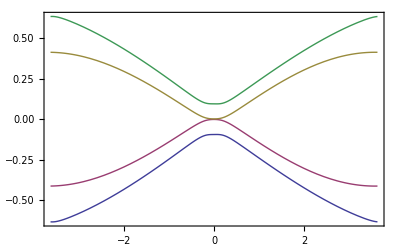
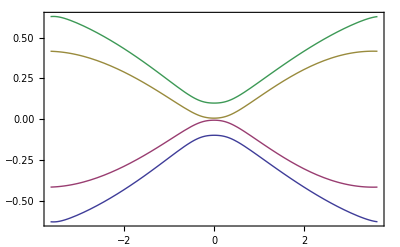
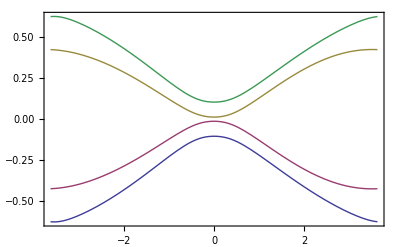
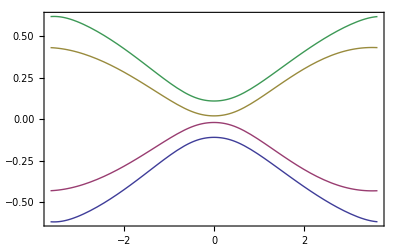
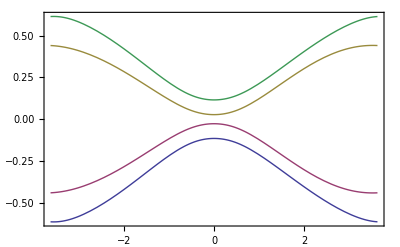

```mathematica
Table[Plot[{EE[i/3,t][[11]],EE[i /3,t][[12]],EE[i/3,t][[13]],EE[i/3,t][[14]]},{t,-2Pi/Sqrt[3],2Pi/Sqrt[3]},Frame->True],{i,1,5}]
```

```mathematica
TT=0.9;
```

```mathematica
Eigensystem[HH[3TT,2.4084167TT]][[1]]
```

{2.7255+1.27531×10^-15 ⅈ,-2.7255-2.74086×10^-16 ⅈ,2.7255-5.55112×10^-17 ⅈ,-2.7255-1.08073×10^-15 ⅈ,2.02199+3.18322×10^-16 ⅈ,2.02199-2.22045×10^-16 ⅈ,-2.02199-2.85168×10^-16 ⅈ,-2.02199+5.84715×10^-16 ⅈ,1.49031+2.29854×10^-16 ⅈ,-1.49031-1.12784×10^-16 ⅈ,1.49031+7.52003×10^-16 ⅈ,-1.49031-8.18663×10^-16 ⅈ,1.21884+1.26635×10^-16 ⅈ,-1.21884-4.08238×10^-16 ⅈ,1.21884+4.12121×10^-16 ⅈ,-1.21884+5.90576×10^-17 ⅈ,-0.881142+1.22125×10^-15 ⅈ,0.881142-4.08744×10^-17 ⅈ,-0.881142-6.245×10^-16 ⅈ,0.881142-2.64834×10^-16 ⅈ,0.013762+7.05878×10^-14 ⅈ,-0.013762-6.94462×10^-14 ⅈ,-0.013762+1.10955×10^-14 ⅈ,0.013762-1.19527×10^-14 ⅈ}

```mathematica
EEE[x_,y_]:={-1-√(3+2 Cos[x Sqrt[3]]+2 Cos[√3 x/2- 3y/2]+2 Cos[Sqrt[3]x/2+3 y/2]),-1+√(3+2 Cos[Sqrt[3]x]+2 Cos[Sqrt[3]x/2-3 y/2]+2 Cos[Sqrt[3]x/2+3 y/2])}
```

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=EEE[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-4.5,2.2},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-4.5,2.2},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

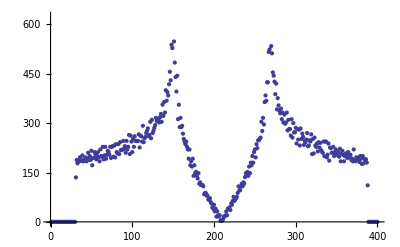

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
```

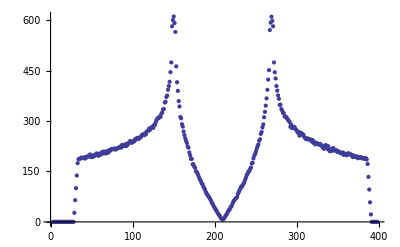

```mathematica
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```

```mathematica
CoefficientArrays[{For[i=1,i≤3,i++,i x+i^2 y+i^3 z==0]},{x,y,z}]
```

{SparseArray[<1>,{1}]}

```mathematica
Normal[%]
```

{{Null}}

```mathematica
For[i=1,i≤3,i++,p[i]=i x+i^2 Exp[I (kx+ky)] y+i^3 z]
```

```mathematica
FINAL=CoefficientArrays[{p[1]==0,p[2]==0,p[3]==0},{x,y,z}][[2]]
```

SparseArray[<9>,{3,3}]

```mathematica
MatrixForm[FINAL]
```

```mathematica
HHH[kx_,ky_]:=({{1, ⅇ^(ⅈ (kx+ky)), 1}, {2, 4 ⅇ^(ⅈ (kx+ky)), 8}, {3, 9 ⅇ^(ⅈ (kx+ky)), 27}})
```

```mathematica
Normal[%]
```

{{0,0,0},{{1,1,1},{2,4,8},{3,9,27}}}

```mathematica
MatrixForm
```